## Visualizing Weather Data

```mathematica
WeatherData["New Delhi", "Temperature"]
```

13 °C

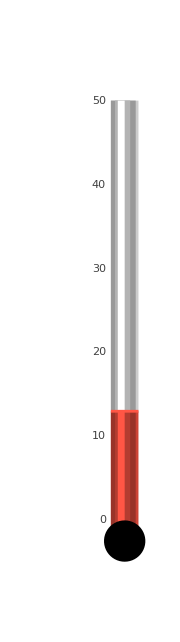

```mathematica
ThermometerGauge[WeatherData["New Delhi", "Temperature"], {0, 50}]
```

```mathematica
Weather = {WeatherData["New Delhi", "WindDirection"], WeatherData["New Delhi", "WindSpeed"]}
```

{210 °,9.36 km/h}

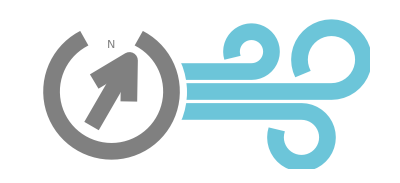

```mathematica
IconData["WindDirection", Weather[[1]]]
```

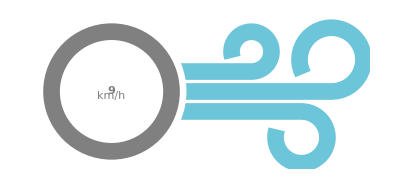

```mathematica
IconData["WindSpeed", Weather[[2]]]
```

```mathematica
DateString[]
```

Wed 29 Dec 2021 11:47:16

```mathematica
Grid[{{"Loc","Temp", "Wind Speed", "Wind Direction", "Time"},
{$GeoLocation, WeatherData[$GeoLocation, "Temperature"],WeatherData[$GeoLocation, "WindSpeed"], WeatherData[$GeoLocation, "WindDirection"], DateString[]}},
Frame-> All]
```

Loc | Temp | Wind Speed | Wind Direction | Time
GeoPosition[{28.63,77.22}] | 13 °C | 9.36 km/h | 210 ° | Wed 29 Dec 2021 11:54:23

## Fitting Wind Data to Distributions

### Getting Data, PDF, CDF, Histogram

TimeSeries[…]

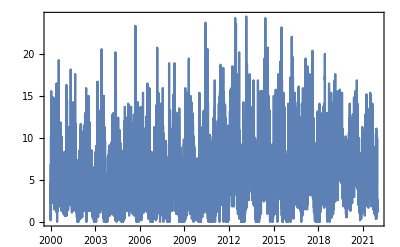

```mathematica
wd = WeatherData["New Delhi","WindSpeed",{{2000,1,1},{2021,12,29},"Day"}, MissingDataMethod-> "Remove"]
DateListPlot[wd]
```

```mathematica
quantities = QuantityMagnitude[wd[[2]][[1]][[1]]];
```

```mathematica
dis =SmoothKernelDistribution[quantities]
```

DataDistribution[…]

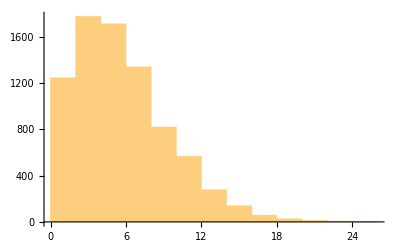

```mathematica
Histogram[quantities]
```

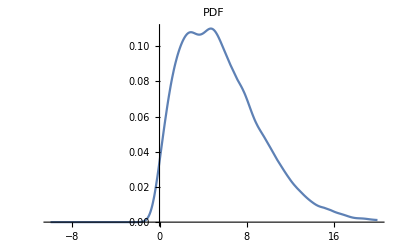
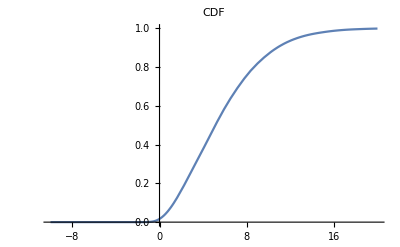

```mathematica
Table[Plot[f[dis, x], {x, -10, 20}, PlotLabel -> f], {f, {PDF, CDF}}]
```

```mathematica
pdf = PDF[dis, x]
```

Piecewise[{{InterpolatingFunction[…][x], -2.78335≤x≤27.2334}, {0, True}}]

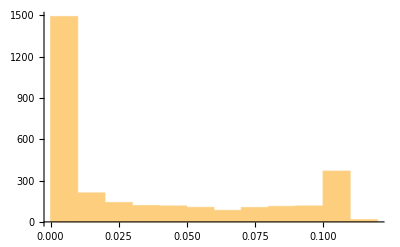

```mathematica
Histogram[InterpolatingFunction[…]/@Range[-2.77, 27.1, 0.01]]
```

```mathematica
cdf = CDF[dis, x]
```

Piecewise[{{1, x>27.2334}, {InterpolatingFunction[…][x], -2.78335≤x≤27.2334}, {0, True}}]

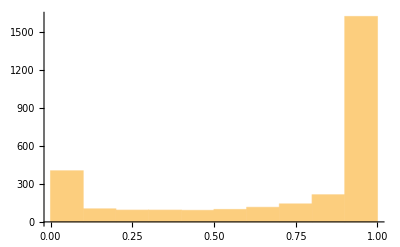

```mathematica
Histogram[InterpolatingFunction[…]/@ Range[-2.7, 27, 0.01]]
```

### Fitting to a parametric distribution(?)

```mathematica
evd = FindDistribution[quantities]
```

ExtremeValueDistribution[3.98471,2.92228]

```mathematica
DistributionFitTest[quantities, evd]
```

0.0000149759

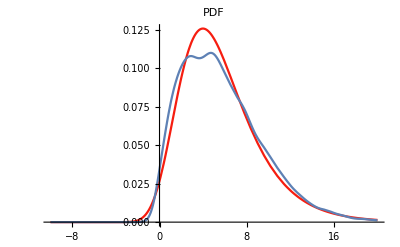

```mathematica
Show[Plot[PDF[evd,x], {x,-10, 20},  PlotLabel -> PDF, ColorFunction->Hue],Plot[PDF[dis, x], {x, -10, 20}, PlotLabel -> PDF]]
```

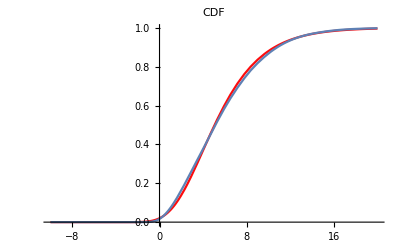

```mathematica
Show[Plot[CDF[evd,x], {x,-10, 20},  PlotLabel -> CDF, ColorFunction->Hue],Plot[CDF[dis, x], {x, -10, 20}, PlotLabel -> CDF]]
```

## Curve Fitting

```mathematica
Population = Entity["Country","India"][]
```

TimeSeries[…]

```mathematica
Targets = QuantityMagnitude[Population[[2]][[1]][[1]]];
Labels = Range[1970, 2020];
```

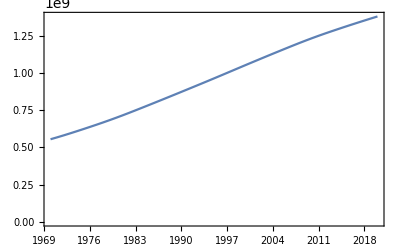

```mathematica
DateListPlot[Population]
```

```mathematica
linearmodel = LinearModelFit[Targets, x, x]
```

FittedModel[5.17702×10^8+1.72412×10^7 x]

```mathematica
linearmodel["ANOVATableMeanSquares"]
```

{3.28469×10^18,7.11242×10^13}

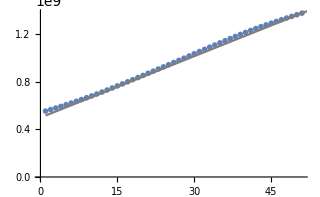

```mathematica
Show[
ListPlot[Targets, PlotMarkers-> "OpenMarkers"],
ListLinePlot[linearmodel[#]&/@Range[0,51], ColorFunction->Hue]
]
```

```mathematica
l = linearmodel[#]&/@ Range[1,51] ;
```

```mathematica
rms= Targets - l// RootMeanSquare
```

8.2665×10^6

```mathematica
mean = Mean[Targets] //N
```

9.65972×10^8

```mathematica
rms / mean
```

0.0085577

```mathematica
nonlinearmodels ={NonlinearModelFit[Targets,a*x*x+b*x+c,{a,b,c},x],
NonlinearModelFit[Targets,a*x*x*x+b*x*x+c*x+d,{a,b,c,d},x],
NonlinearModelFit[Targets,a*x*x*x*x+b*x*x*x+c*x*x+d*x+c,{a,b,c,d,e},x]

}
```

{FittedModel[5.19695×10^8+«22» x+4340.47 x^2],FittedModel[5.44073×10^8+«22» x+«16» x^2-3276.09 x^3],FittedModel[-8.39135×10^6+«22» x-«1»+«18» «1»-1950.41 x^4]}

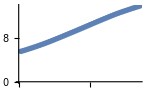
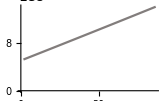
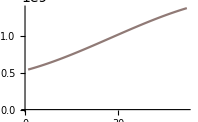
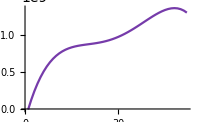

```mathematica
{
ListPlot[Targets, PlotMarkers-> "OpenMarkers"],
ListLinePlot[nonlinearmodels[[1]][#]&/@Range[0,51], ColorFunction->Hue],
ListLinePlot[nonlinearmodels[[2]][#]&/@Range[0,51], ColorFunction->"Rainbow"],
ListLinePlot[nonlinearmodels[[3]][#]&/@Range[0,51], ColorFunction->Hue]
}
```

```mathematica
nl1= nonlinearmodels[[1]][#]&/@ Range[1,51] ;
nl2= nonlinearmodels[[2]][#]&/@ Range[1,51] ;
nl3= nonlinearmodels[[3]][#]&/@ Range[1,51] ;
```

```mathematica
RootMeanSquare/@{l, Targets - nl1,  Targets - nl2,Targets - nl3}
```

```mathematica
{9.987526820133208*^8,8.223639832121042*^6,736265.683734417,9.754310299841043*^7}
```

{9.98753×10^8,8.22364×10^6,736266.,9.75431×10^7}

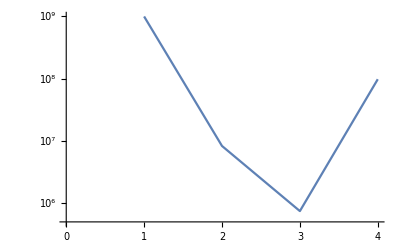

```mathematica
ListLinePlot[{9.987526820133208*^8,8.223639832121042*^6,736265.683734417,9.754310299841043*^7}, ScalingFunctions->"Log"]
```

in conclusion: 
3rd degree model performs the best. 
The 4th degree model does not generalize well as it has far too many parameters for this problem.

## Predicting Wind Speeds

```mathematica
windspeeddata= ResourceData[ResourceObject["Wind Speed Measurements"]] ;
```

```mathematica
i=1;
wsd = i++->#&/@QuantityMagnitude/@Normal[windspeeddata[[All, 2]]]
```

{1→15.04,2→14.71,3→18.5,4→10.58,5→13.33,6→13.21,7→13.5,8→10.96,9→12.58,6557,6567→8.67,6568→7.21,6569→13.83,6570→17.58,6571→13.21,6572→14.,6573→18.5,6574→20.33}
 |  |  |  |

```mathematica
wsd = RandomChoice[wsd, Length[wsd]]
```

{5460→13.62,4417→12.71,1414→22.,4972→9.96,4370→9.87,4753→24.46,1235→8.96,6560,2004→20.5,4253→7.21,345→21.34,2064→13.29,3733→5.63,1395→13.67,5570→7.58}
 |  |  |  |

```mathematica
Length[wsd]
```

6574

```mathematica
train = ResourceFunction["TrainTestSplit"][wsd][[1]];
```

```mathematica
test = ResourceFunction["TrainTestSplit"][wsd][[2]];
```

```mathematica
l= DimensionReduce[wsd]
```

{{0.254406,0.305041},{1.11711,1.34719},6570,{-1.70194,0.535592},{0.197761,2.78578}}
 |  |  |  |

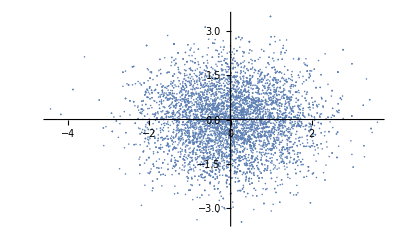

```mathematica
ListPlot[l]
```

```mathematica
ListPlot3D[DimensionReduce[windspeeddata, 3]]
```

-Graphics3D-

```mathematica
predfunc = Predict[train,Method->"NeuralNetwork", TargetDevice->"GPU"]
```

PredictorFunction[…]

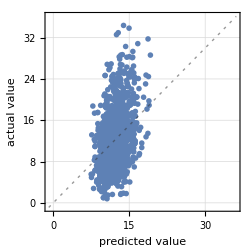
Predictor Measurements
Predictor method | NearestNeighbors
Number of test examples | 1315
Standard deviation | 5.14 ± 0.11
Standard deviation baseline | 5.55 ± 0.12
R-squared | 0.141 ± 0.053
Mean cross entropy | 3.03 ± 0.02
Single evaluation time | 3.05 ms/example
Batch evaluation speed | 2.58 examples/ms
-Graphics- |

```mathematica
PredictorMeasurements[predfunc,test]
```

```mathematica
predfunc = Predict[train,Method->"DecisionTree"]
```

PredictorFunction[…]

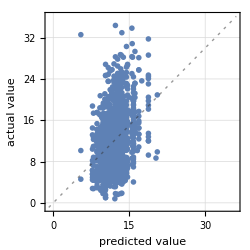
Predictor Measurements
Predictor method | DecisionTree
Number of test examples | 1315
Standard deviation | 5.25 ± 0.12
Standard deviation baseline | 5.55 ± 0.12
R-squared | 0.106 ± 0.057
Mean cross entropy | 3.11 ± 0.059
Single evaluation time | 3.51 ms/example
Batch evaluation speed | 2.19 examples/ms
-Graphics- |

```mathematica
PredictorMeasurements[predfunc,test]
```

```mathematica
predfunc = Predict[train,Method->"NearestNeighbors"]
PredictorMeasurements[predfunc,test]
```

PredictorFunction[…]

Predictor Measurements
Predictor method | NearestNeighbors
Number of test examples | 1315
Standard deviation | 5.14 ± 0.11
Standard deviation baseline | 5.55 ± 0.12
R-squared | 0.141 ± 0.053
Mean cross entropy | 3.03 ± 0.02
Single evaluation time | 2.63 ms/example
Batch evaluation speed | 2.1 examples/ms
-Graphics- |

```mathematica
Information[predfunc]
```

Predictor information
Data type | Numerical
Standard deviation | 5.35 ± 0.087
Method | NearestNeighbors
Single evaluation time | 3.05 ms/example
Batch evaluation speed | 33.7 examples/ms
Loss | 3.12 ± 0.017
Model memory | 193. kB
Training examples used | 5259 examples
Training time | 2.39 s
 |

## Land Surface Classification

```mathematica
SatData = ResourceObject["Sample Data: Satellite"]
```

ResourceObject[…]

```mathematica
SatData = ResourceData[SatData];
```

```mathematica
{Grid[Partition[Values[Normal[SatData[[1]]][[2;;;;3]]],3]],
Grid[Partition[Values[Normal[SatData[[1]]][[3;;;;3]]],3]],
Grid[Partition[Values[Normal[SatData[[1]]][[4;;;;3]]],3]],
Grid[Partition[Values[Normal[SatData[[1]]][[5;;;;3]]],3]],
Normal[SatData[[1]]][[1]]
}
```

{92 | 94 | 106
102 | 101 | 103
118 | 103 | 102
104 | 128 | 107,115 | 84 | 79
102 | 126 | 92
85 | 104 | 126
88 | 100 | 113,120 | 102 | 84
83 | 133 | 112
84 | 81 | 134
121 | 84 | 87,94 | 106 | 102
101 | 103 | 118
103 | 102 | 104,gray soil}

```mathematica
enc = NetEncoder[{"Class", DeleteDuplicates[Normal[SatData[[All,1]]]]}]
```

NetEncoder[<>]

```mathematica
Targets =enc/@Normal[SatData[[Values]][[All,1]]];
```

```mathematica
Features= Normal[SatData[[Values]][[All,2;;]]];
```

```mathematica
listdata= Append[ {Targets[[#]]},Features[[#]]] &/@ Range[Length[Targets]]
```

{{1,{92,115,120,94,84,102,106,79,84,102,102,83,101,126,133,103,92,112,118,85,84,103,104,81,102,126,134,104,88,121,128,100,84,107,113,87}},{1,{84,102,106,79,84,102,102,83,80,102,102,79,92,112,118,85,84,103,104,81,84,99,104,78,88,121,128,100,84,107,113,87,84,99,104,79}},6431,{3,{56,68,87,74,60,71,91,81,60,64,104,99,59,79,89,71,63,79,93,75,63,68,109,92,59,83,96,74,59,83,92,74,59,83,92,70}},{3,{60,71,91,81,60,64,104,99,56,64,108,96,63,79,93,75,63,68,109,92,59,75,109,96,59,83,92,74,59,83,92,70,63,79,108,92}}}
 |  |  |  |

```mathematica
ListPlot[DimensionReduce[listdata[[#]][[2]]]& /@ Range[Length[Targets]]]
```

## Image Classifier

```mathematica
f = ResourceData["FashionMNIST"][[;;128]]
```

{-Graphics-→2,-Graphics-→9,-Graphics-→6,-Graphics-→0,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→5,-Graphics-→4,-Graphics-→8,-Graphics-→0,-Graphics-→8,-Graphics-→9,-Graphics-→0,-Graphics-→2,-Graphics-→2,-Graphics-→9,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→8,-Graphics-→7,-Graphics-→4,-Graphics-→4,-Graphics-→0,-Graphics-→4,-Graphics-→4,-Graphics-→8,-Graphics-→7,-Graphics-→1,-Graphics-→5,-Graphics-→0,-Graphics-→5,-Graphics-→3,-Graphics-→2,-Graphics-→7,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→1,-Graphics-→6,-Graphics-→0,-Graphics-→9,-Graphics-→6,-Graphics-→0,-Graphics-→5,-Graphics-→6,-Graphics-→7,-Graphics-→7,-Graphics-→2,-Graphics-→5,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→1,-Graphics-→4,-Graphics-→9,-Graphics-→8,-Graphics-→3,-Graphics-→4,-Graphics-→5,-Graphics-→5,-Graphics-→6,-Graphics-→3,-Graphics-→5,-Graphics-→8,-Graphics-→5,-Graphics-→9,-Graphics-→8,-Graphics-→1,-Graphics-→2,-Graphics-→8,-Graphics-→1,-Graphics-→3,-Graphics-→6,-Graphics-→8,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→5,-Graphics-→0,-Graphics-→2,-Graphics-→6,-Graphics-→8,-Graphics-→1,-Graphics-→2,-Graphics-→7,-Graphics-→6,-Graphics-→6,-Graphics-→4,-Graphics-→6,-Graphics-→5,-Graphics-→0,-Graphics-→1,-Graphics-→7,-Graphics-→3,-Graphics-→5,-Graphics-→8,-Graphics-→4,-Graphics-→3,-Graphics-→8,-Graphics-→5,-Graphics-→0,-Graphics-→5,-Graphics-→3,-Graphics-→0,-Graphics-→8,-Graphics-→5,-Graphics-→6,-Graphics-→1,-Graphics-→0,-Graphics-→7,-Graphics-→6,-Graphics-→1,-Graphics-→9,-Graphics-→7,-Graphics-→6,-Graphics-→9,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→6,-Graphics-→0,-Graphics-→6,-Graphics-→3,-Graphics-→6,-Graphics-→3,-Graphics-→5}

```mathematica
rf = f[[;;20]]
```

{-Graphics-→2,-Graphics-→9,-Graphics-→6,-Graphics-→0,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→5,-Graphics-→4,-Graphics-→8,-Graphics-→0,-Graphics-→8,-Graphics-→9,-Graphics-→0,-Graphics-→2,-Graphics-→2,-Graphics-→9,-Graphics-→3,-Graphics-→3,-Graphics-→3}

```mathematica
FeatureSpacePlot3D[Keys[rf]]
```

-Graphics3D-

```mathematica
FeatureSpacePlot[Keys[rf]]
```

-Graphics-

```mathematica
net=NetModel["LeNet"];
result=NetTrain[net,f,All]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:586  rounds:293  time:16s  examples/s:2363
data | ,,  training examples:128  processed examples:37504  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.11×10^-4  error:0%
 | 
 | ]

```mathematica
Information[trained]
```

Net Information

```mathematica
result["TrainingNet"]
```

NetGraph[<>]

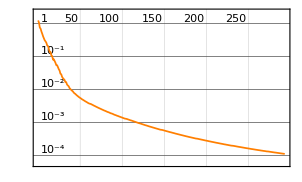
| rounds
loss | -Graphics-

```mathematica
result["LossPlot"]
```